```mathematica
n=50;
qsize=(n+1)^2;
idx[x_,y_]:=(n+1)*x+y+1;
{qrow,qcol,qval} = {Flatten[ConstantArray[0,{qsize*10,1}]],Flatten[ConstantArray[0,{qsize*10,1}]],Flatten[ConstantArray[0,{qsize*10,1}]]};
qnz=0;
For[x=1,x≤n-1,x++,
For[y=0,y≤n,y++,
qnz=qnz+1;
qrow[[qnz]]=idx[x,y];
qcol[[qnz]]=idx[x+1,y];
qval[[qnz]]=b1*x;
]
]
For[x=0,x≤n,x++,
For[y=1,y≤n-1,y++,
qnz=qnz+1;
qrow[[qnz]]=idx[x,y];
qcol[[qnz]]=idx[x,y+1];
qval[[qnz]]=b2*y;
]
]
For[x=1,x≤n,x++,
For[y=0,y≤n-1,y++,
qnz=qnz+1;
qrow[[qnz]]=idx[x,y];
qcol[[qnz]]=idx[x-1,y+1];
qval[[qnz]]=d*x;
]
]
For[x=0,x≤n-1,x++,
For[y=1,y≤n,y++,
qnz=qnz+1;
qrow[[qnz]]=idx[x,y];
qcol[[qnz]]=idx[x+1,y-1];
qval[[qnz]]=d*y;
]
]
For[x=1,x≤n,x++,
For[y=0,y≤n,y++,
qnz=qnz+1;
qrow[[qnz]]=idx[x,y];
qcol[[qnz]]=idx[x-1,y];
qval[[qnz]]=x*(1+2*x-x^2);
]
]
For[x=0,x≤n,x++,
For[y=1,y≤n,y++,
qnz=qnz+1;
qrow[[qnz]]=idx[x,y];
qcol[[qnz]]=idx[x,y-1];
qval[[qnz]]=y*(1+2*y-y^2);
]
]
qr=DeleteCases[qrow,0];
qc=DeleteCases[qcol,0];
qv=qval[[1;;Length[qc]]];
q=SparseArray[Transpose[{qr,qc}]->qv];
q = Transpose[q];
temp = Total[q];
For[i=1,i≤qsize,i++,q[[i]][[i]] = q[[i]][[i]]-temp[[i]];]
q
```

SparseArray[<17698>, {2601, 2601}]

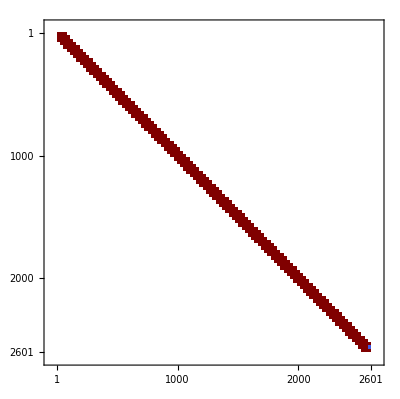

```mathematica
MatrixPlot[q]
```

```mathematica
MatrixPlot
```